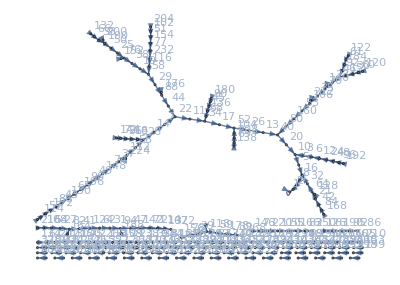

```mathematica
data=Table[
i->If[i==1,1,If[EvenQ[i],i/2,3i+1]]
,{i,238}];
Graph[data,VertexLabels->"Name"]
```